```mathematica
Plot3D[Sin[x+y^2],{x,-3,3},{y,-3,3}
,RegionFunction->Function[{x,y,z},2 x-y + z<0]
(*,Filling->Bottom,
FillingStyle->Directive[Darker[Red],Opacity[1]]
*)
(*,PlotPoints->150*)
(*,BoxRatios->{1,1,1}*)
(*,BoxRatios->{6,8,2}*)
]
```

-Graphics3D-

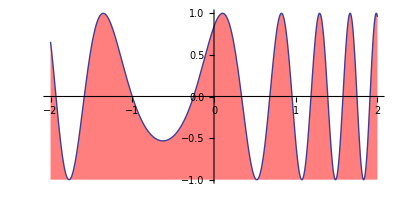

```mathematica
Plot[Sin[x+y^2]//.y->2 x+1,{x,-2,2},Filling->Bottom,FillingStyle->Directive[Red,Opacity[0.5]],AspectRatio->1/2]
```

```mathematica
(*SphericalPlot3D[Sin[x+y^2],{x,0, Pi},{y,0, 2 Pi},RegionFunction->Function[{x,y,z},2 x-y<0],(*Filling->Bottom,FillingStyle->Directive[Red,Opacity[0.6]],*)PlotPoints->150,BoxRatios->{6,8,2}]*)
```

```mathematica
ClearAll[quad, u, v]
quad[u_, v_] := Polygon[{-u-v,u-v,u+v,v-u}] ;
(*quad := Polygon[{-#1-#2,#1-#2,#1+#2,#2-#1}] &;*)
ClearAll[uu,vv]
uu = {1,1,1} ;
vv = {1,-1,-1} ;
n = uu × vv ;

p = Plot3D[  Sqrt[1-x^2/4 - y^2  ], {x,-2, 2}, {y, -1, 1},
PlotRange -> Full,
AxesLabel -> {x,y,z}
,RegionFunction->Function[{x,y,z},n.{x,y,z}<0]
] 
Show[p, Graphics3D[quad[uu,vv]]]
```

-Graphics3D-

-Graphics3D-

```mathematica
(*Table[i Pi/4, {i, 0, 8}]*)

(*Plot3D[  Sqrt[1-x^2 - y^2  ], {x,-1, 1}, {y, -1, 1},
AxesLabel->{x,y, z} ,
Epilog->{
Arrow[{{0,0,0},{1,0,0}}]
}
] 
Plot[  Sqrt[1-x^2  ], {x,-1, 1},
AxesLabel->{x,y} ,
Epilog->{
Arrow[{{0,0},{1,0}}]
}
] *)
```